```mathematica
SetDirectory["~/git/2D_bloch_wave_propagation_metamaterial"];
data = Import["./export/modes.csv"];
MatrixForm@data;

Nc =Dimensions[data][[2]];
```

```mathematica
Table[
ListLinePlot3D[
Transpose[{data[[All, 1]], data[[All, 2]], data[[All, i]]}], AxesLabel->{"k_x/π [-]", "k_y/π [-]","Ω = (ω*l)/c [-] " }, Mesh->None, ImageSize->400, PlotLegends->Automatic, ImageSize->Large, PlotLabel->"Mode "~~ToString[i-2]
],
 {i, 3, Nc}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
grid2 = 
Table[
ListContourPlot3D[
Transpose[{data[[All, 1]], data[[All, 2]], data[[All, i]]}], AxesLabel->{"k_x/π [-]", "k_y/π [-]","Ω = (ω*l)/c [-]" }, Mesh->None, ImageSize->400,  ImageSize->Large, PlotLabel->"Mode "~~ToString[i-2]
],
 {i, 3, Nc}]
Export["./export/img/mathematica/dispersion_surface.pdf",grid2];
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

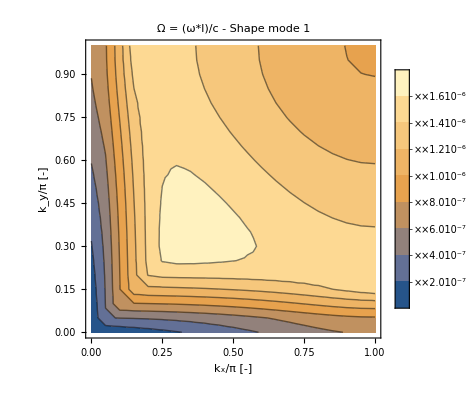
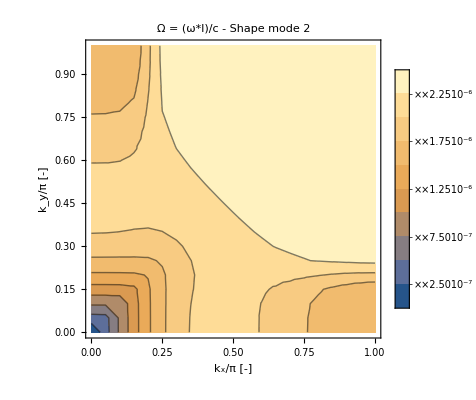
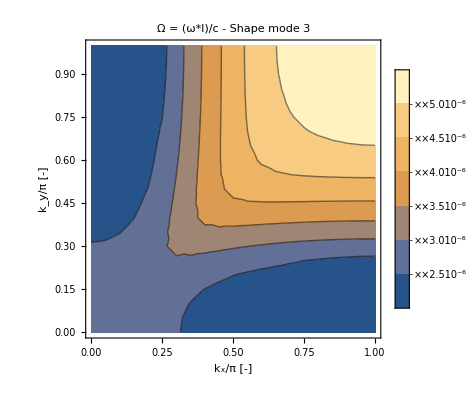
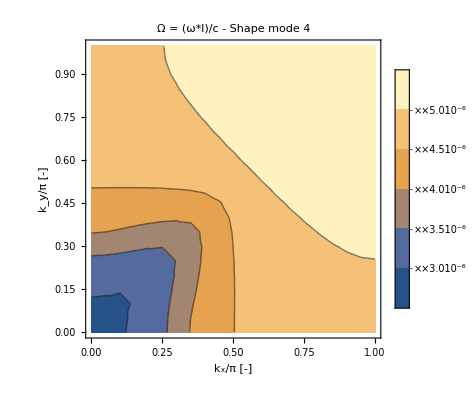
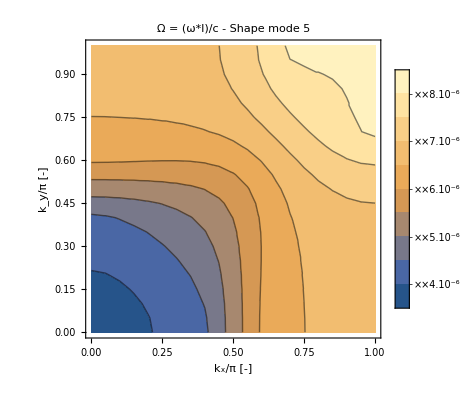
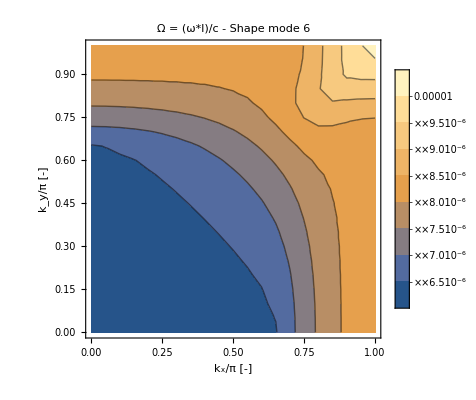
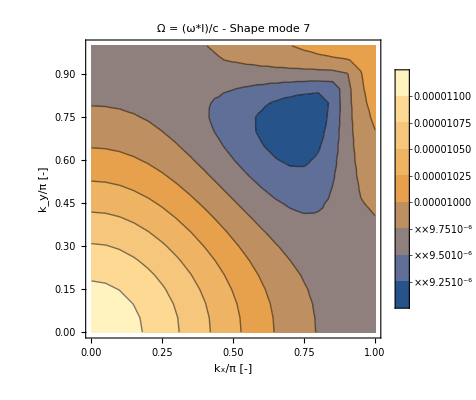
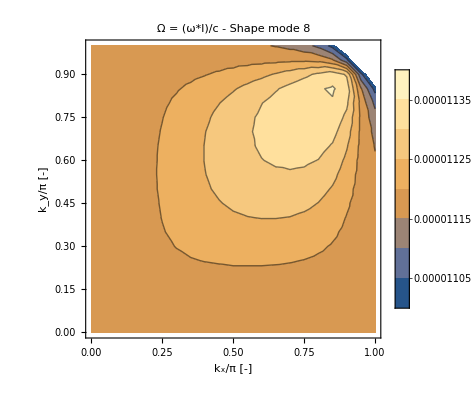

```mathematica
grid3 =
Table[
ListContourPlot[
Transpose[{data[[All, 1]], data[[All, 2]], data[[All, i]]}], FrameLabel->{"k_x/π [-]", "k_y/π [-]"}, Mesh->None, ImageSize->400, PlotLegends->Automatic, ImageSize->Large, PlotLabel->"Ω = (ω*l)/c - Shape mode "~~ToString[i-2]
],
 {i, 3, Nc}]
Export["./export/img/mathematica/contour_plot.pdf",grid3];
```